# Residue Calculus

### More Plotting Stuff

I made another plotting routine.

```mathematica
ReImComplexPlot3D[ f_,{z_,R_}]:=Module[{fTemp,x,y},
fTemp[{x_,y_}]=f/.z->x+I y;
Plot3D[
{Re[fTemp[{x,y}]],Im[fTemp[{x,y}]]},
{x, -R,R},
{y,-R,R},
PlotLegends->{"re","im"}]
]
f[z_]:=ArcTan[z]
TabView[{
"CPlot3D"->ComplexPlot3D[f[z],{z,3}],
"ReImPlot3D"->ReImComplexPlot3D[f[z],{z,3}]
}]
```

12

As a reminder the residue theorem says
	∫_Γ f(z)dz=2π ⅈ   ∑_(j=1)^m w(c_j) r_j
for an analytic function f(z) with singularities at c_1,c_2,…,c_m in Γ. The residues are  r_j=lim_(z→c_j) (z-c_j)f(z) and w is the winding number.
	https://en.wikipedia.org/wiki/Residue_theorem
Chapter 5 is about the techniques that use the residue theorem to compute useful things.

## Special Contours

### Key Hole Contour Ex 5.11 p130

A key hole contour looks like this.  The idea is to let the outer radius R→∞ go and the inner radius ϵ->0^+.  The two horizontal

```mathematica
p1[R_][t_]:=R ⅇ^(2 π ⅈ t)
p2[ϵ_,R_][t_]:=ϵ + (R-ϵ)t +ϵ/2 ⅈ
p3[ϵ_][t_]:=ϵ ⅇ^(-2π ⅈ t)
p4[ϵ_,R_][t_]:= R-(R-ϵ)t -ϵ/2 ⅈ
{ϵ,R}={0.1,1.5};
Pic=ParametricPlot[{
ReIm[p1[R][t]],
ReIm[p2[ϵ,R][t]],
ReIm[p3[ϵ][t]],
ReIm[p4[ϵ,R][t]]},{t,0, 1},
PlotRange->All,
PlotLegends->Automatic];
Manipulate[
Show[Pic,
Epilog->{
{PointSize[0.02], Point[ReIm[{p1[R][t],p2[ϵ,R][t],p3[ϵ][t],p4[ϵ,R][t]}]]},
{White,Rectangle[{0,-ϵ/2},{1.1 ϵ,ϵ/2}],Rectangle[{R-ϵ,-ϵ/2},{R+ϵ,ϵ/2}]}
}],
{{t,0.2},0,1}]
```

Show::gtype: Symbol is not a type of graphics.

The straight line portions of ∮_Γ  cancel unless there is a branch cut along the real axis! if f has no branch cuts then we can be weird and put the branch cut for log along the real axis and
	∫_Γ log(z)f(z)dz=∫_ϵ^R log(x+ϵ ⅈ)f(x+ϵ ⅈ)dx+∫_R^ϵ log(x-ϵ ⅈ)f(x-ϵ ⅈ)dx+∫_Γ_1 log(z)f(z) dz+∫_Γ_3 log(z)f(z)dz.
	
Flipping the order of the limits in the second term gives

∫_Γ log(z)f(z)dz=∫_ϵ^R (log(x+ϵ ⅈ)f(x+ϵ ⅈ)-log(x-ϵ ⅈ)f(x-ϵ ⅈ))dx+∫_Γ_1 log(z)f(z) dz+∫_Γ_3 log(z)f(z)dz

Since f is continuous let ϵ->0^+ and the red term becomes
	∫_0^R (log(x+0^+ ⅈ)-log(x-0^+ⅈ))f(x)dx=∫_0^R (log(x)-(log(x)+2π ⅈ))f(x)dx=2π ⅈ ∫_0^R f(x)dx
As ϵ->0^+ the green term because to zero because dz=ⅈ ϵ π ⅇ^(ⅈ π t) 
	|log(ϵ ⅇ^(i π t))f(ϵ ⅇ^(ⅈ π t))|≈ -log(ϵ)|f(0)|
so 
	|∫_Γ_3 log(z)f(z)dz|≤-ϵ π log(ϵ)|f(0)|→0

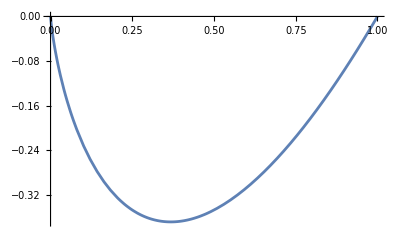

```mathematica
Plot[ ϵ Log[ϵ],{ϵ,0,1}]
```

Putting this together we get
	∮_Γ log(z)f(z)dz=2π ⅈ ∫_0^R f(z)dz+∫_Γ_1 log(z)f(z)dz
If f(z) →0 fast enough as |z|→∞ then ∫_Γ_1 log(z)f(z)dz->0 and we can evaluate
	∫_0^∞ f(z)dz=1/(2π ⅈ)∮_Γ log(z)f(z)dz
using the residue theorem!

### Branch Cuts (Dog Bone Contour) Ex 5.12 p132 e.g. ∫_-1^1 (√(1-x^2))/(1+x^2)dx

```mathematica
f[z_]:=(√(1-z^2))/(1+z^2)
Plot[ f[x], {x, -1,1}];
NIntegrate[f[x],{x,-1,1}]
```

0.+1.30129 ⅈ

```mathematica
f[z_]:=(ⅈ √(z-1)√(z+1))/(1+z^2)
TabView[{
"3D"->ComplexPlot3D[f[z],{z,2},
AxesLabel->{"re","im","abs"},
PlotLegends->Automatic],
"2D"->ComplexPlot[f[z],{z,2},
AxesLabel->{"re","im"},
Epilog->{Arrow[{{-1,0},{1,0}}]},
PlotLegends->Automatic],
"3DReIm"->ReImComplexPlot3D[f[z],{z,2}]}
]
```

123

A dog bone contour looks like this.  The idea is to let the inner radius ϵ->0^+.  The two horizontal

```mathematica
ϵ=0.1;
Manipulate[
{c1,c2}={{0,0},{1,0}};
Graphics[{
{Red,Circle[{0,0},ϵ]},
{Blue, Circle[{1,0},ϵ]},
{White, Rectangle[c1+ϵ{1/(√2),-1/(√2)},c2+ϵ{-1/(√2),1/(√2)}]},
{Green, Line[{c1+ϵ{1/(√2),1/(√2)},c2+ϵ{-1/(√2),1/(√2)}}]},
{Cyan, Line[{c1+ϵ{1/(√2),-1/(√2)},c2+ϵ{-1/(√2),-1/(√2)}}]}
},
Axes->True,
PlotRange->{{-0.2,1.2},{-1,1}}],
{{ϵ,0.1},0,0.2}]
```